```mathematica
ClearAll["Global`*"]
Λ=4.0;m=1.0;L=50.0;
S1=(Sqrt[3]/2)*Sqrt[m*Λ^5];
M1=Sqrt[4/3*Λ^5/m];
S2=-S1;
M2=-M1;
eps=10^-1
```

1/10

```mathematica
equations={
Sr'[z]==Re[(2/3)*(0.5*Log[(Sr[z]*Mr[z]-Si[z]*Mi[z])^2+(Sr[z]*Mi[z]+Si[z]*Mr[z])^2]-5*Log[Λ])],

(*Si'[z]==Re[-(2/3)*Arg[(Sr[z]+I*Si[z])*(Mr[z]+I*Mi[z])]]*)(*Si'[z]==0*)
Si'[z]==-(2/3)*((Im[(Sr[z]+I*Si[z])*(Mr[z]+I*Mi[z])]/Re[(Sr[z]+I*Si[z])*(Mr[z]+I*Mi[z])])+2Pi),

Mr'[z]==Re[(2/3)*Re[(Sr[z]+I*Si[z])/(Mr[z]+I*Mi[z])]-(1/2)*m],

Mi'[z]==Re[-(2/3)*Im[(Sr[z]+I*Si[z])/(Mr[z]+I*Mi[z])]]
};
```

```mathematica
boundaryConditions={
Sr[-L]==S1-eps,Si[-L]==0,
Mr[-L]==M1-eps,Mi[-L]==0(*,

Sr[L]==S2,Si[L]==0,
Mr[L]==M2,Mi[L]==0*)
};
```

```mathematica
(*Solve the system uSing shooting method*)

sol=NDSolve[Join[equations, boundaryConditions],{Sr[z],Si[z],Mr[z],Mi[z]},{z,-L,L}(*Method->{"Shooting","StartingInitialConditions"->{Sr[-L]==S1,Si[-L]==0,
Mr[-L]==M1,Mi[-L]==0,Sr[L]==S2,Si[L]==0,
Mr[L]==M2,Mi[L]==0,Sr'[-L]==0.1,(*Initial guess for derivatives*)
Si'[-L]==0.1,
Mr'[-L]==0.1,
Mi'[-L]==0.1},
"MaxIterations"->500}*)];
```

NDSolve::ndcf: Repeated convergence test failure at z == 23.1822; unable to continue.

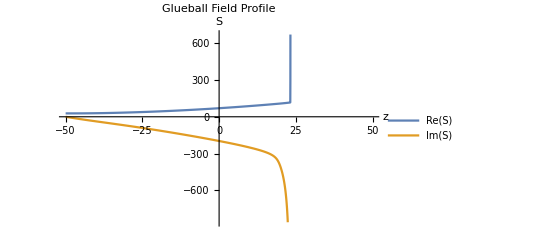

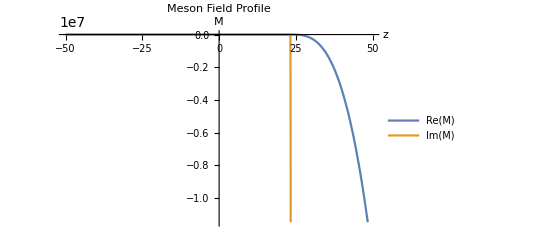

```mathematica
Plot[Evaluate[{Sr[z],Si[z]}/. sol],{z,-L,L},PlotLegends->{"Re(S)","Im(S)"},PlotLabel->"Glueball Field Profile",AxesLabel->{"z","S"}]
Plot[Evaluate[{Mr[z],Mi[z]}/. sol],{z,-L,L},PlotLegends->{"Re(M)","Im(M)"},PlotLabel->"Meson Field Profile",AxesLabel->{"z","M"}]
```

```mathematica
sol
```

{{Sr[z]→InterpolatingFunction[…][z],Si[z]→InterpolatingFunction[…][z],Mr[z]→InterpolatingFunction[…][z],Mi[z]→InterpolatingFunction[…][z]}}

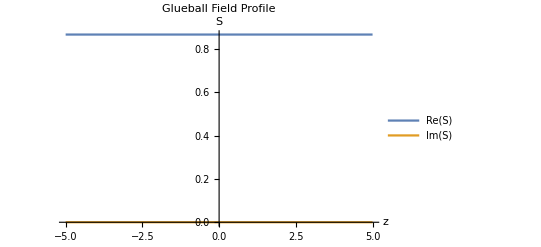

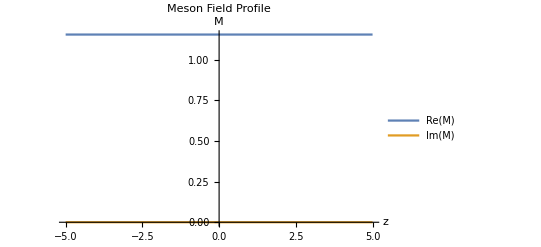

```mathematica
(*Define parameters and vacuum solutions*)ClearAll["Global`*"];
Λ=1;(*Dynamical scale*)m=1;(*Quark mass*)L=5;(*Start with smaller domain*)(*Compute vacuum solutions*)S1=(Sqrt[3]/2)*Sqrt[m*Λ^5];
M1=Sqrt[4/3*Λ^5/m];
S2=-S1;
M2=-M1;

(*Define the system of ODEs*)
eqns={Sr'[z]==Re[(2/3)*(0.5*Log[(Sr[z]*Mr[z]-Si[z]*Mi[z])^2+(Sr[z]*Mi[z]+Si[z]*Mr[z])^2]-5*Log[Λ])],Si'[z]==-(2/3)*Im[(Sr[z]+I*Si[z])*(Mr[z]+I*Mi[z])]/Re[(Sr[z]+I*Si[z])*(Mr[z]+I*Mi[z])],Mr'[z]==(2/3)*(Sr[z]*Mr[z]+Si[z]*Mi[z])/(Mr[z]^2+Mi[z]^2)-m/2,Mi'[z]==-(2/3)*(Si[z]*Mr[z]-Sr[z]*Mi[z])/(Mr[z]^2+Mi[z]^2),(*Boundary conditions*)Sr[-L]==S1,Si[-L]==0,Mr[-L]==M1,Mi[-L]==0(*,Sr[L]==S2,Si[L]==0,Mr[L]==M2,Mi[L]==0*)};

(*Solve using shooting method with better initial guesses*)
sol=NDSolve[eqns,{Sr,Si,Mr,Mi},{z,-L,L},Method->{"Shooting","StartingInitialConditions"->{Sr[-L]==S1,Si[-L]==0,Mr[-L]==M1,Mi[-L]==0,(*Add small non-zero derivatives to prevent constant solution*)Sr'[-L]==(S2-S1)/(2*L),(*Approximate slope*)Si'[-L]==0,Mr'[-L]==(M2-M1)/(2*L),(*Approximate slope*)Mi'[-L]==0},"MaxIterations"->1000},PrecisionGoal->8,AccuracyGoal->8];

(*Plot the solutions*)
Plot[Evaluate[{Sr[z],Si[z]}/. sol],{z,-L,L},PlotLegends->{"Re(S)","Im(S)"},PlotLabel->"Glueball Field Profile",AxesLabel->{"z","S"}]

Plot[Evaluate[{Mr[z],Mi[z]}/. sol],{z,-L,L},PlotLegends->{"Re(M)","Im(M)"},PlotLabel->"Meson Field Profile",AxesLabel->{"z","M"}]
```